### Old

```mathematica
ParametricPlot3D[
	{ArcCosh[y] - Sqrt[1-1/y^2], 1/y Cos[x], 1/y Sin[x]},
	{x,0,2Pi},{y,1,10},PlotRange->All,PlotPoints->{15,60}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{s-Tanh[s],Cos[x]Sech[s],Sin[x]Sech[s]},
	{s,0,5},{x,0,2Pi}]
```

-Graphics3D-

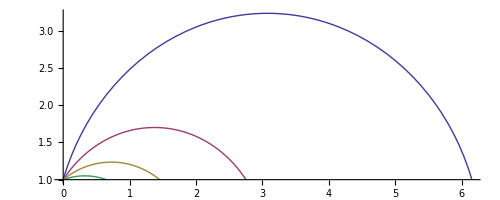

```mathematica
ParametricPlot[Evaluate[
	Table[
		{Cot[phi],0}+Csc[phi]
			{Cos[#],Sin[#]}&[th phi +(1-th)(Pi-phi)],
		{phi,Pi/10,4Pi/10,Pi/10}]],
		{th,0,1},AspectRatio->Automatic]
```

```mathematica
{Cot[phi],0}+Csc[phi] *
			{Cos[#],Sin[#]}&[th phi +(1-th)(Pi-phi)]
```

```mathematica
{Cot[phi] + Cos[(-phi + Pi) (1 - th) + phi th] Csc[phi], 
 
  Csc[phi] Sin[(-phi + Pi) (1 - th) + phi th]}
```

```mathematica
phi=π/20;ParametricPlot3D[Evaluate[{s-Tanh[s],1.005 Cos[x+π/2] Sech[s],1.005 Sin[x+π/2] Sech[s],{Hue[0.1]}}/.{s->ArcCosh[Csc[phi] Sin[(-phi+π) (1-th)+phi th]],x->Cot[phi]+Cos[(-phi+π) (1-th)+phi th] Csc[phi]}],{th,0.001,1},Prolog->{Thickness[0.4]},Lighting->None]
```

-Graphics3D-

```mathematica
Show[%61,%74,%8,Boxed->False,Axes->False]
```

```mathematica
circlearc[width_,radius_,tmax_]:=
 {Circle[{0,0},radius,{0,tmax}],Line[{{radius,0},{radius-width,0}}],
 Circle[{0,0},radius-width,{0,tmax}],
 Line[# {Cos[tmax],Sin[tmax]}& /@ {radius,radius-width}]}
```

```mathematica
tmax=2 π;width=0.09;Show[GraphicsGrid[glist=Table[tmax=(1-width) tmax;Graphics[circlearc[width,1,tmax],AspectRatio->Automatic,PlotRange->{{-1,1},{-1,1}}],{i,1,5},{j,1,5}]]]
```

### New

The above parametrization takes x+iy in the upper half plane directly to the pseudosphere, but lengths are necessarily distorted along its length. This rectifies that:

```mathematica
γ={ ArcTanh[√(1-E^(-2u))]-√(1-E^(-2u)),E^(-u)};
```

This is constant length:

```mathematica
√(D[γ,u].D[γ,u])//Simplify
```

1

The pseudosphere itself is

```mathematica
S=γ.{{1,0,0},{0,Cos[v],Sin[v]}};
```

```mathematica
ParametricPlot3D[S,{u,0,3},{v,0,2Pi},PlotRange->All,Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
phi=π/20;

S2={ArcCosh[u]-(√(-1+u^2))/u,1/u}.{{1,0,0},{0,Cos[v],Sin[v]}};;

ParametricPlot3D[Evaluate[S2/.{u->Csc[phi] Sin[(-phi+π) (1-th)+phi th],v->Cot[phi]+Cos[(-phi+π) (1-th)+phi th] Csc[phi]}],{th,0.001,1},Lighting->None]
```

-Graphics3D-

```mathematica
Show[%41,%61]
```

-Graphics3D-

Here we plot h-equidistant lines in the upper half plane, on the pseudosphere, showing that the parametrization S is correct.

```mathematica
Show[
ParametricPlot3D[S2/.{u->#[[2]],v->#[[1]]}&/@Table[{2Pi t,E^(h+.02)},{h,0,3,.2}],
{t,0,1},PlotRange->All],

ParametricPlot3D[S,{u,0,3},{v,0,2Pi},PlotRange->All,Mesh->{14,10},
Boxed->False,Axes->False]
,Boxed->False,Axes->False]
```

-Graphics3D-

Here we plot e-equidistant lines in the upper half plane, on the pseudosphere, showing that the other parametrization S2 is correct.

```mathematica
Show[
ParametricPlot3D[S2/.{u->#[[2]],v->#[[1]]}&/@Table[{2Pi t,h+.02},{h,1,Cosh[3],(Cosh[3]-1)/15}],
{t,0,1},PlotRange->All],

ParametricPlot3D[S2,{u,1,Cosh[3]},{v,0,2Pi},PlotRange->All,Mesh->{14,10},
Boxed->False,Axes->False]
,Boxed->False,Axes->False]
```

-Graphics3D-

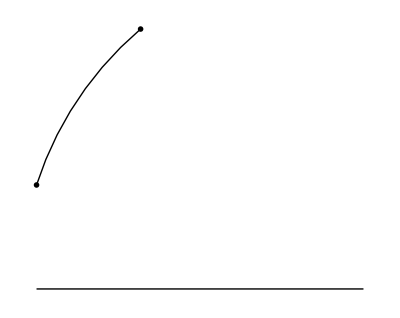

```mathematica
vvv={0,2};
www={2,5};

Show[Graphics[{
Line[{{0,0},{2Pi,0}}],
PointSize[.01],,
Point/@{vvv,www},UpPlaneArc[{vvv,www}]}]]
```

```mathematica
UpPlaneArc[{v_,w_}]:=Circle[#,(√(#1.#1)&)[#-v],

If[#[[1]]<0,Pi+ArcTan[#[[2]]/#[[1]]],ArcTan[#[[2]]/#[[1]]]]&/@

If[v[[1]]>w[[1]],{v-#,w-#},{w-#,v-#}]


]&@{(v.v-w.w)/(2 (v⟦1⟧-w⟦1⟧)),0}
```

```mathematica
CircleToParam[Circle[center_,radius_,{start_,stop_}]]:=center+radius{Cos[#],Sin[#]}&@(start (1-t)+stop t)
```

```mathematica
Show[
ParametricPlot3D[S2/.{u->#[[2]],v->#[[1]]}&/@
{CircleToParam[UpPlaneArc[{vvv,www}]]},
{t,0,1},PlotRange->All,PlotStyle->Directive[Red,Thick]],

ParametricPlot3D[S,{u,0,3},{v,0,2Pi},PlotRange->All,Mesh->{14,11},
Boxed->False,Axes->False]
,Boxed->False,Axes->False]
```

-Graphics3D-

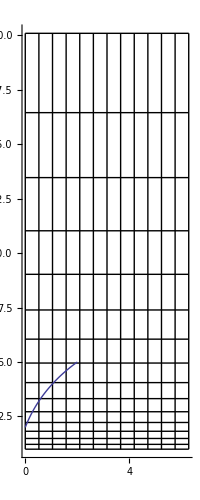

```mathematica
Show[Graphics[
{Table[Line[{{0,E^h},{2Pi,E^h}}],{h,0,3,.2}],
Table[Line[{{h,1},{h,E^3}}],{h,0,2Pi,2Pi/12}]}],
ParametricPlot[CircleToParam[UpPlaneArc[{vvv,www}]],{t,0,1}],Axes->True
]
```